```mathematica
Quit[];
```

```mathematica
SetOptions[EvaluationNotebook[],ShowGroupOpener->True]
```

## Load packages (run this)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$LoadFeynArts=True;
Global`$LoadAddOns={"FeynHelpers"};
<<FeynCalc`;
$FAVerbose = 0;

FAPatch[PatchModelsOnly->True];
```

Optional::opdef: The default value for the optional argument TraditionalForm`cc1_ : DiracGamma(h : 6 | 7)\ cc2_. contains a pattern.

General::stop: Further output of Optional :: opdef will be suppressed during this calculation.

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

FeynHelpers 1.1.0 loaded.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

Patching FeynArts models... done!

## Diagram and amplitude utilities (run this)

### Functions for generating diagrams

```mathematica
exclusions={V[1],V[2]};

frModelName="EFT_MeV_DM_pseudoscalar";
model={frModelName<>"/"<>frModelName};
genericModel={"Lorentz",frModelName<>"/"<>frModelName};

insertionLevel={Particles};
```

```mathematica
genDiags[inFields_,outFields_,nLoops_:0,adj_:{3,4,5},otherExclusions_:{}]:=Block[{tops},
tops=CreateTopologies[nLoops, Length[inFields]-> Length[outFields],ExcludeTopologies-> {Tadpoles,SelfEnergies,WFCorrections},Adjacencies-> adj];
InsertFields[tops,inFields-> outFields,InsertionLevel-> insertionLevel,Model-> model,GenericModel-> genericModel,ExcludeParticles-> Join[exclusions,otherExclusions]]
]
```

### Abbreviations for states

```mathematica
stateπ0=S[1];
stateπm=S[2];
stateπp=-S[2];
statek0=S[3];
statek0bar=-S[3];
statekm=S[4];
statekp=-S[4];
stateη=S[5];
stateγ=V[1];
stateν=F[1];
stateνbar=-F[1];
statel=F[2];
statelbar=-F[2];
statex=F[3];
statexbar=-F[3];
statep=S[7];

mesonList={stateπ0,stateπp,stateπm,statekp,statekm,statek0,statek0bar,stateη};
```

### Function for creating amplitudes

Photon momentum should always be k

```mathematica
createAmp[diags_,inmomenta_,outmomenta_,lorentzIndices_,truncated_:False]:=Module[{amp},
(*Compute the diagram*)
amp=CreateFeynAmp[diags, PreFactor->-ⅈ,Truncated-> truncated,GaugeRules->{}];
amp=FCFAConvert[amp,
IncomingMomenta-> inmomenta,
OutgoingMomenta-> outmomenta,
LorentzIndexNames-> lorentzIndices,
LoopMomenta->{l}, 
UndoChiralSplittings->True,
List->False,
SMP-> True,
ChangeDimension-> 4,
FinalSubstitutions-> M$FACouplings,
TransversePolarizationVectors->{k}];

Simplify[ExpandScalarProduct[DiracSimplify[Contract[amp],DiracSubstitute67-> True]]]
]
```

### For writing to python files

```mathematica
dotProdsToStrings[expr_]:=expr//ReplaceAll[#,Pair[Momentum[pA_], Momentum[pB_]]:>ToExpression[ToString[pA]<>"DOT"<>ToString[pB]]]&
```

```mathematica
pyDir=NotebookDirectory[]<>"/python/";
```

### Compute 2→2 cross section

The differential cross section is
	dσ=1/((2 E_A)(2 E_B)|v_A-v_B|)|ℳ|^2 dΠ_LIPS,
where for m_A=m_B the prefactor is equal to:

```mathematica
xSecPrefactor[mA_]:=1/((2 Q/2)^2 2(√(Q^2/4-mA^2)/√(Q^2/4)))
```

This function computes the cross section by integrating over cos θ

```mathematica
getXSec[amp_,mIn_,m1_,m2_]:=1/(16π)(2pOut)/(√s) xSecPrefactor[mIn] Integrate[amp/.t->m1^2+mx^2-2(1/2 √(s(pOut^2+m1^2))-pOut √(s/4-mx^2)cθ),{cθ,-1,1}]/.{pOut->(√(s^2+(m1^2-m2^2)^2-2 s (m1^2+m2^2)))/(2 √s)}//Simplify
```

This function computes the cross section by integrating over t. Letting m_1=m_2=m and the final state particles’ masses be m_3 and m_4, we have
	dt/dc_θ=p_1 p_3
	⇒ σ=1/(16π Q^2(Q^2-4 m_1^2))∫ dt |ℳ|^2

```mathematica
xSectIntegralFactor2body[mIn_,Q_]:=1/2 1/(8π Q^2(Q^2-4 mIn^2))
```

Returns t_min,t_max

```mathematica
tIntegralBounds2Body[mIn_,m3_,m4_,Q_]:={(m3^2 Q+m4^2 Q+2 mIn^2 Q-Q^3-√(-4 mIn^2+Q^2) √(m3^4+(m4^2-Q^2)^2-2 m3^2 (m4^2+Q^2)))/(2 Q),(m3^2 Q+m4^2 Q+2 mIn^2 Q-Q^3+√(-4 mIn^2+Q^2) √(m3^4+(m4^2-Q^2)^2-2 m3^2 (m4^2+Q^2)))/(2 Q)}
```

```mathematica
xSectIntegral2body[msqrd_,mIn_,m3_,m4_,Q_]:=Module[{tIndefInt,tMin,tMax},
tIndefInt=Integrate[msqrd,t];
{tMin,tMax}=tIntegralBounds2Body[mIn,m3,m4,Q];
xSectIntegralFactor2body[mIn,Q]((tIndefInt/.t->tMax)-(tIndefInt/.t->tMin))
]
```

### Width prefactor

This is valid when both final state particles have mass m

```mathematica
widthFactor[m_]:=1/(2mp)1/(16 π^2)4π (√(mp^2/4-m^2))/mp
```

### Set scalar’s gauge parameter to one

```mathematica
GaugeXi[S[7]]=1
```

1

### Substitute in for unstable mediator propagator

```mathematica
substituteUnstablePPropagator[expr_,moms_]:=expr/.FeynAmpDenominator[PropagatorDenominator[Total[Momentum/@moms], mp]]:>1/(SP[Total[Momentum/@moms]]-mp^2+ⅈ widthp mp)//ScalarProductExpand
```

### Determine integration bounds for t

Returns t_min,t_max

```mathematica
tIntegralBounds3Body[s_,m1_,m2_,m3_,Q_]:=Module[{termA,termB,result},
termA = (m2-m3) (m2+m3) (m1-Q) (m1+Q)+(m1^2+m2^2+m3^2+Q^2) s-s^2;
termB = √(m2^4+(m3^2-s)^2-2 m2^2(m3^2+s)) √(m1^4+(Q^2-s)^2-2 m1^2(Q^2+s));

result = {1/(2 s) (termA - termB), 1/(2 s) (termA + termB)}//Simplify[#,Assumptions->{s>Q^2>0,Q>0}]&
]
```

## χ̄ χ→P P

```mathematica
ampSquaredxbarxtopp=Module[{fs,diags,amp,ampSquared},
ClearScalarProducts[];
SetMandelstam[Q^2,t,u,pxbar,px,-p1,-p2,mx,mx,mp,mp];

diags=genDiags[{statexbar,statex},{statep,statep}];

amp=createAmp[diags,{pxbar,px},{p1,p2},{μ,ν}]//PropagatorDenominatorExplicit;

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//FermionSpinSum[#,ExtraFactor->1/4]&//ReplaceAll[#,DiracTrace->Tr]&//Contract;
ampSquared=ampSquared/.u->2(mp^2+mx^2)-Q^2-t;

1/2 ampSquared/.{cosbeta->Cos[β],sinbeta->Sin[β]}//Series[#,{β,0,2}]&//Normal//Simplify(* since final state contains identical particles *)
]
```

((2 β^2-1) gpxx^4 (mp^4+2 mp^2 (mx^2-t)+(mx^2-t) (mx^2-Q^2-t)) (-2 mp^2-2 mx^2+Q^2+2 t)^2)/(4 (mx^2-t)^2 (-2 mp^2-mx^2+Q^2+t)^2)

```mathematica
$Assumptions={Q>0,1>4rx>0,1>4rp>0};

xSectIntegral2body[ampSquaredxbarxtopp,mx,mp,mp,Q];

%/.{mx->rx Q,mp->rp Q}//Simplify//StandardForm
```

1/(64 Q^2 (π-4 π rx^2))gpxx^4 (-1+2 β^2) (4 √((1-4 rp^2) (1-4 rx^2))-(4 rp^4)/(1-2 rp^2+√((-1+4 rp^2) (-1+4 rx^2)))-(4 rp^4)/(-1+2 rp^2+√((-1+4 rp^2) (-1+4 rx^2)))+((1-4 rp^2+6 rp^4) Log[-1/2 Q^2 (1-2 rp^2+√((-1+4 rp^2) (-1+4 rx^2)))])/(-1+2 rp^2)+((1-4 rp^2+6 rp^4) Log[1/2 Q^2 (1-2 rp^2+√((-1+4 rp^2) (-1+4 rx^2)))])/(-1+2 rp^2)-((1-4 rp^2+6 rp^4) Log[-1/2 Q^2 (-1+2 rp^2+√((-1+4 rp^2) (-1+4 rx^2)))])/(-1+2 rp^2)-((1-4 rp^2+6 rp^4) Log[1/2 Q^2 (-1+2 rp^2+√((-1+4 rp^2) (-1+4 rx^2)))])/(-1+2 rp^2))

Need to simplify logs by hand

```mathematica
xSecxbarxtopp=1/(64 Q^2 (π-4 π rx^2))gpxx^4 (-1+2 β^2) (FullSimplify[4 √((1-4 rp^2) (1-4 rx^2))-(4 rp^4)/(1-2 rp^2+√((-1+4 rp^2) (-1+4 rx^2)))-(4 rp^4)/(-1+2 rp^2+√((-1+4 rp^2) (-1+4 rx^2)))]+FullSimplify[((1-4 rp^2+6 rp^4) Log[-1/2 Q^2 (1-2 rp^2+√((-1+4 rp^2) (-1+4 rx^2)))])/(-1+2 rp^2)+((1-4 rp^2+6 rp^4) Log[1/2 Q^2 (1-2 rp^2+√((-1+4 rp^2) (-1+4 rx^2)))])/(-1+2 rp^2)-((1-4 rp^2+6 rp^4) Log[-1/2 Q^2 (-1+2 rp^2+√((-1+4 rp^2) (-1+4 rx^2)))])/(-1+2 rp^2)-((1-4 rp^2+6 rp^4) Log[1/2 Q^2 (-1+2 rp^2+√((-1+4 rp^2) (-1+4 rx^2)))])/(-1+2 rp^2)])
```

((2 β^2-1) gpxx^4 ((2 √((4 rp^2-1) (4 rx^2-1)) (3 rp^4-8 rp^2 rx^2+2 rx^2))/(rp^4-4 rp^2 rx^2+rx^2)+(2 (6 rp^4-4 rp^2+1) (2 tanh^-1((1-2 rp^2)/(√((4 rp^2-1) (4 rx^2-1))))+ⅈ π))/(2 rp^2-1)))/(64 Q^2 (π-4 π rx^2))

```mathematica
FortranForm[xSecxbarxtopp/.β->beta]>>(pyDir<>"xsec_xx_to_pp.py")
```

```mathematica
$Assumptions=True;
```

# Factorized processes

## DM + propagator part

```mathematica
ampSqrdxbarxtopProp=Module[{is,diags,amp,ampSquared},
is={statexbar,statex};

ClearScalarProducts[];
SP[pxbar,pxbar]=mx^2;
SP[px,px]=mx^2;
SP[pxbar,px]=Q^2/2-mx^2;

diags=genDiags[is,{statep}];
(*Paint[diags,ColumnsXRows->{1,1}];*)

amp=createAmp[diags,{pxbar,px},{P},{μ,ν}]//PropagatorDenominatorExplicit;

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//FermionSpinSum[#,ExtraFactor->1/4]&//ReplaceAll[#,DiracTrace->Tr]&//Contract;
1/((Q^2-mp^2)^2+mp^2 widthp^2)ampSquared/.{cosbeta->Cos[β],sinbeta->Sin[β]}//Series[#,{β,0,2}]&//Simplify
]
```

(gpxx^2 Q^2)/(2 ((mp^2-Q^2)^2+mp^2 widthp^2))-(β^2 (gpxx^2 Q^2))/(2 ((mp^2-Q^2)^2+mp^2 widthp^2))+O(β^3)

## ℓ̄ ℓ

### P→ℓ̄ ℓ

```mathematica
ampSqrdptolbarl=Module[{fs,diags,amp,ampSquared},
fs={statelbar,statel};

ClearScalarProducts[];
SP[p1,p1]=ml^2;
SP[p2,p2]=ml^2;
SP[p1,p2]=Q^2/2-ml^2;
SP[P,P]=Q^2;

diags=genDiags[{statep},fs];
(*Paint[diags,ColumnsXRows->{1,1}];*)

amp=createAmp[diags,{P},{p1,p2},{μ,ν}]//PropagatorDenominatorExplicit;

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//FermionSpinSum//ReplaceAll[#,DiracTrace->Tr]&//Contract;
ampSquared/.{cosbeta->Cos[β],sinbeta->Sin[β]}//Series[#,{β,0,2}]&//Normal//Simplify
]
```

-2 (β^2-1) gpll^2 Q^2

```mathematica
widthptolbarl=widthFactor[ml]ampSqrdptolbarl/.Q->mp/.ml->rf mp//FullSimplify[#,Assumptions->mp>0]&
```

-((β^2-1) gpll^2 mp √(1-4 rf^2))/(8 π)

```mathematica
FortranForm[widthptolbarl/.β->beta]>>(pyDir<>"width_p_to_ll.py")
```

### χ̄ χ→ℓ̄ ℓ

```mathematica
xSecxbarxtolbarl=4π 1/(64 π^2 Q^2)(√(Q^2/4-ml^2))/(√(Q^2/4-mx^2))ampSqrdxbarxtopProp ampSqrdptolbarl/.s->Q^2/.ml->rf Q/.mx->rx Q/.{cosbeta->Cos[β],sinbeta->Sin[β]}//Series[#,{β,0,2}]&//Normal//FullSimplify[#,Assumptions->Q>0]&
```

((1-2 β^2) gpll^2 gpxx^2 Q^2 √(1-4 rf^2))/(16 π √(1-4 rx^2) ((mp^2-Q^2)^2+mp^2 widthp^2))

```mathematica
FortranForm[xSecxbarxtolbarl/.β->beta]>>(pyDir<>"xsec_xx_to_p_to_ll.py")
```

## P→χ̄ χ

```mathematica
widthptoxbarx=Module[{fs,diags,amp,ampSquared},
fs={statexbar,statex};

ClearScalarProducts[];
SP[p1,p1]=mx^2;
SP[p2,p2]=mx^2;
SP[p1,p2]=Q^2/2-mx^2;
SP[P,P]=Q^2;

diags=genDiags[{statep},fs];
(*Paint[diags,ColumnsXRows->{1,1}];*)

amp=createAmp[diags,{P},{p1,p2},{μ,ν}]//PropagatorDenominatorExplicit;

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//FermionSpinSum[#,ExtraFactor->1/4]&//ReplaceAll[#,DiracTrace->Tr]&//Contract;
widthFactor[mx]ampSquared/.{cosbeta->Cos[β],sinbeta->Sin[β]}//Series[#,{β,0,2}]&//Normal//Simplify
]
```

-((β^2-1) gpxx^2 Q^2 √(mp^2-4 mx^2))/(32 π mp^2)

```mathematica
widthptoxbarx=widthptoxbarx/.Q->mp/.mx->rx mp//FullSimplify[#,Assumptions->mp>0]&
```

-((β^2-1) gpxx^2 mp √(1-4 rx^2))/(32 π)

```mathematica
FortranForm[widthptoxbarx/.β->beta]>>(pyDir<>"width_p_to_xx.py")
```

## γγ

```mathematica
ampSqrdptogg=Module[{fs,diags,amp,ampSquared},
fs={stateγ,stateγ};

ClearScalarProducts[];
SP[p1,p1]=0;
SP[p2,p2]=0;
SP[p1,p2]=Q^2/2;
SP[P,P]=Q^2;

diags=genDiags[{statep},fs];
(*Paint[diags,ColumnsXRows->{1,1}];*)

amp=createAmp[diags,{P},{p1,p2},{μ,ν}]//PropagatorDenominatorExplicit;
(* Replace the ϵ symbol *)
amp=amp/.{P->p1+p2}/.{FALeviCivita->Eps,FAFourVector->Momentum};

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//FermionSpinSum[#,ExtraFactor->1/4]&//ReplaceAll[#,DiracTrace->Tr]&//DoPolarizationSums[#,p1,0]&//DoPolarizationSums[#,p2,0]&//Contract;
ampSquared/.{cosbeta->Cos[β],sinbeta->Sin[β]}//Series[#,{β,0,2}]&//Normal//FullSimplify//Factor
]
```

(alphaEM^2 Q^4 (-β gpFF+gpFF+β vh) (β gpFF+gpFF+β vh))/(8 π^2 vh^2)

```mathematica
widthptogg=widthFactor[0]ampSqrdptogg/.Q->mp//FullSimplify[#,Assumptions->mp>0]&
```

(alphaEM^2 mp^3 (-β gpFF+gpFF+β vh) (β (gpFF+vh)+gpFF))/(128 π^3 vh^2)

```mathematica
xSecxbarxtoptogg=4π 1/(64 π^2 Q^2)(Q/2)/(√(Q^2/4-mx^2))ampSqrdxbarxtopProp ampSqrdptogg/.mx->rx Q//Series[#,{β,0,2}]&//Normal//FullSimplify[#,Assumptions->Q>0]&
```

(alphaEM^2 gpxx^2 Q^4 ((1-2 β^2) gpFF^2+2 β gpFF vh+β^2 vh^2))/(256 π^3 √(1-4 rx^2) vh^2 ((mp^2-Q^2)^2+mp^2 widthp^2))

```mathematica
FortranForm[widthptogg/.β->beta]>>(pyDir<>"width_p_to_gg.py")
FortranForm[xSecxbarxtoptogg/.β->beta]>>(pyDir<>"xsec_xx_to_p_to_gg.py")
```

## π^0 π^0 π^0

|ℳ|^2 for P->π0π0π0

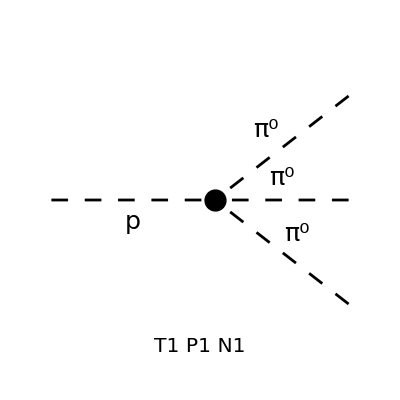

(b0^2 ((10 β^2-1) (-fpi^2) (vh (gpdd-gpuu)+gpGG (mdq-muq))^2-2 β fpi vh (mdq+muq) (vh (gpdd-gpuu)+gpGG (mdq-muq))+β^2 vh^2 (mdq+muq)^2))/(fpi^4 vh^2)

```mathematica
ampSqrdptoπ0π0π0=Module[{fs,diags,amp,ampSquared},
fs={stateπ0,stateπ0,stateπ0};

ClearScalarProducts[];
SP[p1,p1]=mpi0^2;
SP[p2,p2]=mpi0^2;
SP[p3,p3]=mpi0^2;
SP[P,P]=Q^2;

diags=genDiags[{statep},fs];
Paint[diags,ColumnsXRows->{1,1}];

amp=createAmp[diags,{P},{p1,p2,p3},{μ,ν}]//PropagatorDenominatorExplicit;

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//FermionSpinSum//ReplaceAll[#,DiracTrace->Tr]&//Contract;
ampSquared/.{cosbeta->Cos[β],sinbeta->Sin[β]}//Series[#,{β,0,2}]&//Normal//FullSimplify
]
```

```mathematica
ampSqrdptoπ0π0π0/.β->0
```

(b0^2 (vh (gpdd-gpuu)+gpGG (mdq-muq))^2)/(fpi^2 vh^2)

|ℳ|^2 for xx->P->π0π0π0

```mathematica
ampSqrdxbarxtoptoπ0π0π0=ampSqrdxbarxtopProp ampSqrdptoπ0π0π0/.{cosbeta->Cos[β],sinbeta->Sin[β]}//Series[#,{β,0,2}]&//Normal//FullSimplify
```

-(b0^2 gpxx^2 Q^2 ((11 β^2-1) fpi^2 (vh (gpdd-gpuu)+gpGG (mdq-muq))^2+2 β fpi vh (mdq+muq) (vh (gpdd-gpuu)+gpGG (mdq-muq))-β^2 vh^2 (mdq+muq)^2))/(2 fpi^4 vh^2 ((mp^2-Q^2)^2+mp^2 widthp^2))

Perform phase space integration using
	dΠ_LIPS=1/(16 (Q^2(2π))^3)ds dt.

```mathematica
ampSqrdptoπ0π0π0ds=Module[{tdef,tindef,sindef,tMin,tMax},
{tMin,tMax}=tIntegralBounds3Body[s,mpi0,mpi0,mpi0,Q];

tindef=1/(16 Q^2(2π)^3)Integrate[ampSqrdptoπ0π0π0,t];
tdef=(tindef/.t->tMax)-(tindef/.t->tMin)//Simplify
];
```

Width

```mathematica
dwidthdsptoπ0π0π0=1/(2mp)ampSqrdptoπ0π0π0ds/.Q->mp//Simplify
```

-(b0^2 √(s (s-4 mpi0^2)) √(mp^4-2 mp^2 (mpi0^2+s)+(mpi0^2-s)^2) ((10 β^2-1) fpi^2 (vh (gpdd-gpuu)+gpGG (mdq-muq))^2+2 β fpi vh (mdq+muq) (vh (gpdd-gpuu)+gpGG (mdq-muq))-β^2 vh^2 (mdq+muq)^2))/(256 π^3 fpi^4 mp^3 s vh^2)

Cross section

```mathematica
dxSecdsxbarxtoptoπ0π0π0=xSecPrefactor[mx]ampSqrdxbarxtopProp ampSqrdptoπ0π0π0ds/.{cosbeta->Cos[β],sinbeta->Sin[β]}//Series[#,{β,0,2}]&//Normal//Simplify[#,Assumptions->Q>0]&
```

-(b0^2 gpxx^2 √(s (s-4 mpi0^2)) √(mpi0^4-2 mpi0^2 (Q^2+s)+(Q^2-s)^2) ((11 β^2-1) fpi^2 (vh (gpdd-gpuu)+gpGG (mdq-muq))^2+2 β fpi vh (mdq+muq) (vh (gpdd-gpuu)+gpGG (mdq-muq))-β^2 vh^2 (mdq+muq)^2))/(512 π^3 fpi^4 Q s vh^2 √(Q^2-4 mx^2) (mp^4+mp^2 (widthp^2-2 Q^2)+Q^4))

```mathematica
FortranForm[dwidthdsptoπ0π0π0/.β->beta]>>(pyDir<>"dwidth_ds_p_to_pi0pi0pi0.py")
FortranForm[dxSecdsxbarxtoptoπ0π0π0/.β->beta]>>(pyDir<>"dxsec_ds_xx_to_p_to_pi0pi0pi0.py")
```

## π^0 π^+π^-

|ℳ|^2 for P->π0π+π-

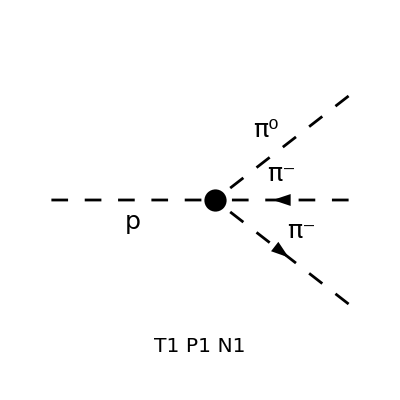

(b0^2 (vh (gpdd-gpuu)+gpGG (mdq-muq))^2)/(9 fpi^2 vh^2)+(β^2 (4 vh^2 (-b0 (mdq+muq)+2 mpi^2+mpi0^2-3 s)^2-16 b0^2 fpi^2 (vh (gpdd-gpuu)+gpGG (mdq-muq))^2))/(36 fpi^4 vh^2)-(2 β b0 (b0 (mdq+muq)-2 mpi^2-mpi0^2+3 s) (vh (gpdd-gpuu)+gpGG (mdq-muq)))/(9 fpi^3 vh)

```mathematica
ampSqrdptoπ0ππ=Module[{fs,diags,amp,ampSquared},
fs={stateπ0,stateπp,stateπm};

ClearScalarProducts[];
SP[p0,p0]=mpi0^2;
SP[pp,pm]=s/2-mpi^2;
SP[pp,p0]=(t-mpi^2-mpi0^2)/2;
SP[pm,p0]=(u-mpi^2-mpi0^2)/2;
SP[pp,pp]=mpi^2;
SP[pm,pm]=mpi^2;
SP[P,P]=Q^2;

diags=genDiags[{statep},fs];
Paint[diags,ColumnsXRows->{1,1}];

amp=createAmp[diags,{P},{p0,pp,pm},{μ,ν}]//PropagatorDenominatorExplicit;

ampSquared=amp*FCRenameDummyIndices[ComplexConjugate[amp]];
ampSquared=ampSquared//FermionSpinSum//ReplaceAll[#,DiracTrace->Tr]&//Contract;
ampSquared=ampSquared/.{P->pp+pm+p0}//ScalarProductExpand;
ampSquared=ampSquared/.u->2 mpi^2+mpi0^2-s-t;
ampSquared/.{cosbeta->Cos[β],sinbeta->Sin[β]}//Series[#,{β,0,2}]&//FullSimplify//Normal
]
```

|ℳ|^2 for xx->P->π0π+π-

```mathematica
ampSqrdxbarxtoptoπ0ππ=ampSqrdxbarxtopProp ampSqrdptoπ0ππ/.{cosbeta->Cos[β],sinbeta->Sin[β]}//Series[#,{β,0,2}]&//Normal//FullSimplify
```

1/(72 fpi^4 vh^2 ((mp^2-Q^2)^2+mp^2 widthp^2))gpxx^2 Q^2 (β^2 (4 vh^2 (-b0 (mdq+muq)+2 mpi^2+mpi0^2-3 s)^2-20 b0^2 fpi^2 (vh (gpdd-gpuu)+gpGG (mdq-muq))^2)+4 b0^2 fpi^2 (vh (gpdd-gpuu)+gpGG (mdq-muq))^2-8 β b0 fpi vh (b0 (mdq+muq)-2 mpi^2-mpi0^2+3 s) (vh (gpdd-gpuu)+gpGG (mdq-muq)))

Perform phase space integration using
	dΠ_LIPS=1/(16 (Q^2(2π))^3)ds dt.

```mathematica
ampSqrdptoπ0ππds=Module[{tdef,tindef,sindef,tMin,tMax},
{tMin,tMax}=tIntegralBounds3Body[s,mpi0,mpi,mpi,Q];

tindef=1/(16 Q^2(2π)^3)Integrate[ampSqrdptoπ0ππ,t];
tdef=(tindef/.t->tMax)-(tindef/.t->tMin)//Simplify
];
```

```mathematica
dwidthdsptoπ0ππ=1/(2mp)ampSqrdptoπ0ππds/.Q->mp//Simplify
```

1/(2304 π^3 fpi^4 mp^3 s vh^2)√(s (s-4 mpi^2)) √(mp^4-2 mp^2 (mpi0^2+s)+(mpi0^2-s)^2) (b0^2 ((4 β^2-1) (-fpi^2) (vh (gpdd-gpuu)+gpGG (mdq-muq))^2-2 β fpi vh (mdq+muq) (vh (gpdd-gpuu)+gpGG (mdq-muq))+β^2 vh^2 (mdq+muq)^2)+2 β b0 vh (2 mpi^2+mpi0^2-3 s) (fpi (vh (gpdd-gpuu)+gpGG (mdq-muq))-β vh (mdq+muq))+β^2 vh^2 (2 mpi^2+mpi0^2-3 s)^2)

```mathematica
dxSecdsxbarxtoptoπ0ππ=xSecPrefactor[mx]ampSqrdxbarxtopProp ampSqrdptoπ0ππds/.{cosbeta->Cos[β],sinbeta->Sin[β]}//Series[#,{β,0,2}]&//Normal//Simplify[#,Assumptions->Q>0]&
```

1/(4608 π^3 fpi^4 Q s vh^2 √(Q^2-4 mx^2) (mp^4+mp^2 (widthp^2-2 Q^2)+Q^4))gpxx^2 √(s (s-4 mpi^2)) √(mpi0^4-2 mpi0^2 (Q^2+s)+(Q^2-s)^2) (b0^2 ((5 β^2-1) (-fpi^2) (vh (gpdd-gpuu)+gpGG (mdq-muq))^2-2 β fpi vh (mdq+muq) (vh (gpdd-gpuu)+gpGG (mdq-muq))+β^2 vh^2 (mdq+muq)^2)+2 β b0 vh (2 mpi^2+mpi0^2-3 s) (fpi (vh (gpdd-gpuu)+gpGG (mdq-muq))-β vh (mdq+muq))+β^2 vh^2 (2 mpi^2+mpi0^2-3 s)^2)

```mathematica
FortranForm[dwidthdsptoπ0ππ/.β->beta]>>(pyDir<>"dwidth_ds_p_to_pi0pipi.py")
FortranForm[dxSecdsxbarxtoptoπ0ππ/.β->beta]>>(pyDir<>"dxsec_ds_xx_to_p_to_pi0pipi.py")
```

# Scratch

```mathematica
(eps/(mp^2-mpi0^2)==β//Solve[#,gpGG]&)⟦1⟧
```

{gpGG→-(vh (b0 fpi gpdd-b0 fpi gpuu+β mp^2-β mpi0^2))/(b0 fpi (mdq-muq))}

```mathematica
eps = b0 fpi (gpuu-gpdd+(muq-mdq)/vh gpGG);
gpGGSub=(eps/(mp^2-mpi0^2)==β//Solve[#,gpGG]&)⟦1⟧;

ampSqrdptogg/.gpGGSub//Series[#,{β,0,2}]&//FullSimplify
ampSqrdptoπ0π0π0/.gpGGSub//Series[#,{β,0,2}]&//FullSimplify
ampSqrdptoπ0ππ/.gpGGSub//Series[#,{β,0,2}]&//FullSimplify
```

(alphaEM^2 gpFF^2 Q^4)/(8 π^2 vh^2)+(alphaEM^2 β gpFF Q^4)/(4 π^2 vh)+(alphaEM^2 β^2 Q^4 (vh^2-gpFF^2))/(8 π^2 vh^2)+O(β^3)

(β^2 (b0 (mdq+muq)+mp^2-mpi0^2)^2)/fpi^4+O(β^3)

(β^2 (b0 (mdq+muq)+mp^2-2 (mpi^2+mpi0^2)+3 s)^2)/(9 fpi^4)+O(β^3)

```mathematica
ampSqrdptoπ0ππ
```

(b0^2 (vh (gpdd-gpuu)+gpGG (mdq-muq))^2)/(9 fpi^2 vh^2)+(β^2 (4 vh^2 (-b0 (mdq+muq)+2 mpi^2+mpi0-3 s)^2-16 b0^2 fpi^2 (vh (gpdd-gpuu)+gpGG (mdq-muq))^2))/(36 fpi^4 vh^2)-(2 β b0 (b0 (mdq+muq)-2 mpi^2-mpi0+3 s) (vh (gpdd-gpuu)+gpGG (mdq-muq)))/(9 fpi^3 vh)

```mathematica
eps=b0 fpi
```

```mathematica
ampSqrdptoπ0ππ/ampSqrdptoπ0π0π0/.{β->0}//FullSimplify
ampSqrdptogg/ampSqrdptoπ0π0π0/.{β->0, gpFF->0}//FullSimplify
```

1/9

0

```mathematica
ampSqrdptogg/.β->0
```

(alphaEM^2 gpFF^2 Q^4)/(8 π^2 vh^2)